```mathematica
(*How can seeded deterministic generator give rise to intermittent multiscale processes *)
```

```mathematica
{{ClearAll[caStep,caUniform,caGaussian,standardize,ar1,dyadicField,generateMarket];

(*1. Deterministic Rule-30 engine*)
caStep[state_List,rule_Integer:30]:=MapThread[BitGet[rule,4 #1+2 #2+#3]&,{RotateRight[state],state,RotateLeft[state]}];
caUniform[n_Integer?Positive,seed_Integer,width_Integer:127,burnIn_Integer:512]:=Module[{state,bits=53},state=IntegerDigits[Abs[seed]+1,2,width];
Do[state=caStep[state],{burnIn}];
Table[state=caStep[state];
(FromDigits[Take[RotateLeft[state,Mod[37 t+seed,width]],bits],2]+1/2)/2^bits,{t,n}]//N];
caGaussian[n_,seed_]:=Sqrt[2.] InverseErf[2 caUniform[n,seed]-1];

(*2. Temporal and multiscale components*)(_□)_□standardize[x_List]:=(x-Mean[x])/StandardDeviation[x];
ar1[x_List,persistence_]:=Rest@FoldList[persistence #1+Sqrt[1-persistence^2] #2&,0.,x];
dyadicField[n_,scale_,seed_,persistence_]:=Module[{coarse},coarse=caGaussian[Ceiling[n/scale]+2,seed];
coarse=standardize@ar1[coarse,persistence];
standardize@Take[Flatten[ConstantArray[#,scale]&/@coarse],n]];

(*3. Turbulence core plus market adapter*)
generateMarket[n_Integer?Positive,seed_Integer,levels_Integer:9,intermittency_:0.35,persistence_:0.70,annualizedVolatility_:0.20,initialPrice_:100.]:=Module[{innovations,fields,logVolatility,relativeVolatility,dailyVolatility,returns,logPrices},innovations=standardize@caGaussian[n,seed+7919];
fields=Table[dyadicField[n,2^(level-1),seed+104729 level,persistence],{level,levels}];
logVolatility=intermittency Total[fields]/Sqrt[levels];
relativeVolatility=Exp[logVolatility];
relativeVolatility/=Mean[relativeVolatility];
dailyVolatility=annualizedVolatility/Sqrt[252.];
(* returns=dailyVolatility standardize[relativeVolatility innovations]; *)
scaleToRMS[x_List,target_]:=target x/Sqrt[Mean[x^2]];
       returns=scaleToRMS[relativeVolatility innovations,dailyVolatility];
logPrices=Log[initialPrice]+Accumulate[returns];
<|"Returns"->returns,"Prices"->Exp[logPrices],"LogPrices"->logPrices,"Volatility"->dailyVolatility relativeVolatility,"Innovation"->innovations,"LogVolatility"->logVolatility,"ScaleFields"->fields|>];}, {□}}
```

{{Null^8 (Null_□)_□},{□}}

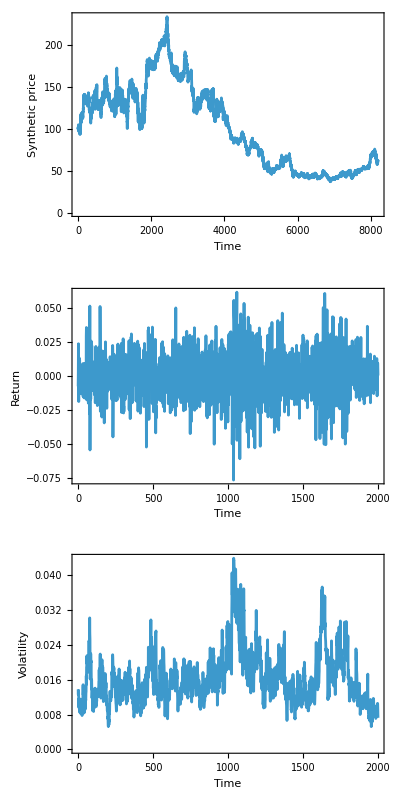

```mathematica
(*Running scenario above*)
market=generateMarket[8192,20260817,10,0.38,0.72];
GraphicsGrid[{{ListLinePlot[market["Prices"],Frame->True,FrameLabel->{"Time","Synthetic price"}]},{ListLinePlot[Take[market["Returns"],2000],PlotRange->All,Frame->True,FrameLabel->{"Time","Return"}]},{ListLinePlot[Take[market["Volatility"],2000],PlotRange->All,Frame->True,FrameLabel->{"Time","Volatility"}]}}]
```

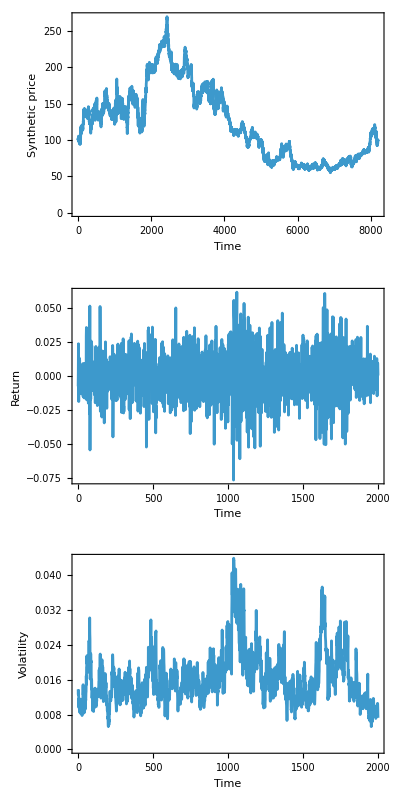

```mathematica
(*Exact reproducability results check*)
market2=generateMarket[8192,20260817,10,0.38,0.72];(_□)_(((□_□)_□)_□)market["Returns"]===market2["Returns"]
```

```mathematica
(*----------Export current experiment----------*)runParameters=<|"Seed"->20260817,"Length"->Length[market["Returns"]],"Levels"->10,"Intermittency"->0.38,"Persistence"->0.72,"AnnualizedVolatility"->0.20,"InitialPrice"->100.|>;

runID=StringJoin["seed-",ToString[runParameters["Seed"]],"-",DateString[{"Year","Month","Day","-","Hour","Minute","Second"}]];

exportDirectory=FileNameJoin[{NotebookDirectory[],"exports",runID}];

CreateDirectory[exportDirectory,CreateIntermediateDirectories->True];

(*Exact Wolfram-format result,including ScaleFields*)
wxfFile=FileNameJoin[{exportDirectory,"market-result.wxf"}];

Export[wxfFile,market,"WXF"];

(*Portable tabular representation*)
csvData=Prepend[Transpose[{Range[Length[market["Returns"]]],market["Returns"],market["Volatility"],market["LogPrices"],market["Prices"]}],{"Time","Return","Volatility","LogPrice","Price"}];

csvFile=FileNameJoin[{exportDirectory,"market-series.csv"}];
Export[csvFile,csvData,"CSV"];

(*Save the generator used for this run*)
definitionFile=FileNameJoin[{exportDirectory,"generator-definition.wl"}];

Save[definitionFile,{caStep,caUniform,caGaussian,standardize,ar1,dyadicField,generateMarket}];

(*Summary statistics*)
returns=market["Returns"];

summary=<|"MeanReturn"->Mean[returns],"ReturnStandardDeviation"->StandardDeviation[returns],"ReturnSkewness"->Skewness[returns],"ReturnKurtosis"->Kurtosis[returns],"ExcessKurtosis"->Kurtosis[returns]-3,"MinimumReturn"->Min[returns],"MaximumReturn"->Max[returns],"AbsoluteReturnLag1Correlation"->Correlation[Most[Abs[returns]],Rest[Abs[returns]]],"FinalPrice"->Last[market["Prices"]],"MinimumPrice"->Min[market["Prices"]],"MaximumPrice"->Max[market["Prices"]]|>;

Export[FileNameJoin[{exportDirectory,"summary.json"}],summary,"JSON"];

metadata=<|"RunID"->runID,"ExportedAt"->DateString["ISODateTime"],"WolframVersion"->$Version,"SystemID"->$SystemID,"Parameters"->runParameters|>;

Export[FileNameJoin[{exportDirectory,"metadata.json"}],metadata,"JSON"];

(*Export plots*)
pricePlot=ListLinePlot[market["Prices"],Frame->True,FrameLabel->{"Time","Synthetic price"},PlotTheme->"Scientific",ImageSize->Large];

dynamicsPlot=GraphicsGrid[{{ListLinePlot[Take[market["Returns"],UpTo[2000]],PlotRange->All,Frame->True,FrameLabel->{"Time","Return"}]},{ListLinePlot[Take[market["Volatility"],UpTo[2000]],PlotRange->All,Frame->True,FrameLabel->{"Time","Volatility"}]}},ImageSize->Large];

Export[FileNameJoin[{exportDirectory,"price-path.png"}],pricePlot,ImageResolution->180];

Export[FileNameJoin[{exportDirectory,"returns-volatility.png"}],dynamicsPlot,ImageResolution->180];

Export[FileNameJoin[{exportDirectory,"results.pdf"}],GraphicsColumn[{pricePlot,dynamicsPlot}]];

(*Integrity hashes*)
filesToHash=FileNames[All,exportDirectory];

hashes=AssociationMap[IntegerString[FileHash[#,"SHA256"],16,64]&,filesToHash];

Export[FileNameJoin[{exportDirectory,"sha256.json"}],hashes,"JSON"];

SystemOpen[exportDirectory];
exportDirectory
```

/home/vinayakarora/Working-Dir/Turbulence/exports/seed-20260817-20260817-131106